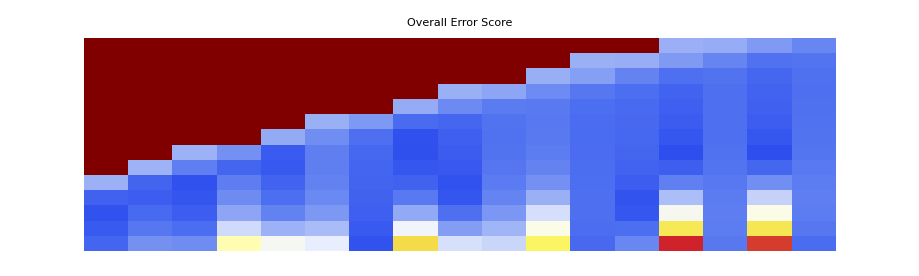
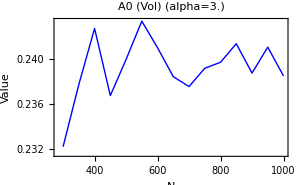
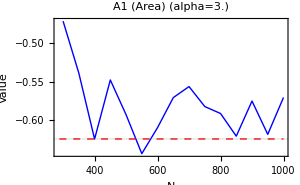
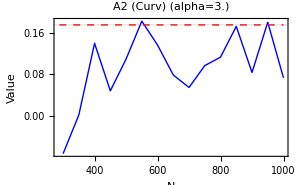

```mathematica
Clear["Global`*"];

(*1. Daten laden*)
eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\data\\eigenvalues\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1000.txt";
eigAll=Import[eigenvalueFilePath,"Table"]//Flatten//N//Sort;

(*Ziele*)
targetA0=0.244038;
targetA1=-0.623796;
targetA2bar=0.175364;

(*Parameter-Scan*)
nRange=Range[200,1000,50];
alphaRange=Range[0.6,6.0,0.4];
betaFix=0.12;
nT=80;
ridge=1.*10^-4;

fitOne[N_Integer,alpha_?NumericQ]:=Module[{eig,λN,λ1,tMin,tMax,tGrid,b,i0,i1,i2,vec0,vec1,vec2,vecC,M,A,rhs,x,A0,A1,A2H,A2bar,score},eig=eigAll[[1;;N]];
λ1=eigAll[[1]];
λN=Last[eig];
tMin=alpha/λN;
tMax=betaFix/λ1;
If[tMax<=tMin,Return[Null]];
tGrid=Exp@Subdivide[Log[tMin],Log[tMax],nT];
b=Total[Exp[-eig #]]&/@tGrid;
i0[t_]:=t^(-3/2) Gamma[3/2,t λN];
i1[t_]:=Exp[-t λN]/t;
i2[t_]:=t^(-1/2) Gamma[1/2,t λN];
vec0=(3 Sqrt[Pi]/4) tGrid^(-3/2)-(3/2) (i0/@tGrid);
vec1=tGrid^(-1)-(i1/@tGrid);
vec2=(Sqrt[Pi]/2) tGrid^(-1/2)-(1/2) (i2/@tGrid);
vecC=ConstantArray[1.,Length[tGrid]];
M=Transpose[{vec0,vec1,vec2,vecC}];
A=Join[M,Sqrt[ridge] IdentityMatrix[4]];
rhs=Join[b,ConstantArray[0.,4]];
x=LeastSquares[A,rhs];
{A0,A1,A2H,A2bar}={x[[1]],x[[2]],x[[3]],x[[3]]/2};
score=Sqrt[((A0-targetA0)/targetA0)^2+((A1-targetA1)/targetA1)^2+((A2bar-targetA2bar)/targetA2bar)^2];
<|"N"->N,"alpha"->alpha,"A0"->A0,"A1"->A1,"A2bar"->A2bar,"score"->score|>];

(*Scan ausführen*)
scan=Flatten[Table[fitOne[n,a],{n,nRange},{a,alphaRange}]];
scan=DeleteCases[scan,Null];

(*Besten Parameter finden*)
best=First@MinimalBy[scan,#score&];
alphaBest=best["alpha"];

(*Heatmap Daten*)
scoreMatrix=Table[SelectFirst[scan,(#["N"]==n&&#["alpha"]==a)&,<|"score"->Indeterminate|>]["score"],{a,Reverse[alphaRange]},{n,nRange}];

(*Grafik-Einstellungen*)
optGeneral={ImageSize->300,LabelStyle->{FontSize->10},Frame->True};

pHeat=ArrayPlot[scoreMatrix,ColorFunction->"TemperatureMap",FrameLabel->{"N Eigenvalues","alpha (tMin)"},FrameTicks->{{Thread[{Range[Length[alphaRange]],Reverse[alphaRange]}],None},{Thread[{Range[Length[nRange]],nRange}],None}},PlotLabel->"Overall Error Score",ImageSize->920,AspectRatio->0.3,ColorFunctionScaling->True];

lineData=SortBy[Select[scan,#["alpha"]==alphaBest&],#["N"]&];

mkPlot[key_,target_,label_]:=ListLinePlot[Table[{d["N"],d[key]},{d,lineData}],PlotRange->All,GridLines->{None,{target}},PlotStyle->{Thick,Blue},PlotLabel->label<>" (alpha="<>ToString[alphaBest]<>")",Epilog->{Red,Dashed,Line[{{nRange[[1]],target},{nRange[[-1]],target}}]},optGeneral,FrameLabel->{"N","Value"}];

pA0=mkPlot["A0",targetA0,"A0 (Vol)"];
pA1=mkPlot["A1",targetA1,"A1 (Area)"];
pA2=mkPlot["A2bar",targetA2bar,"A2 (Curv)"];

(*Zusammenbau*)
Column[{pHeat,Row[{pA0,pA1,pA2},Spacer[10]]},Alignment->Center,Spacings->2]
```